## Bayesian Statistics, Assignment for Friday, Nov. 15

## Reading

Study Chapter 10! Once again, I find the jargon a little out of control. There is no need to introduce the term “hyperparameters.” Of course, different parameters in a problem are used in different ways, but we don’t need to give each use a different term. So, Donovan and Mickey’s new term “hyperparameters” refers to parameters in the prior. The important thing is that they have introduced a new and convenient prior, the “beta distribution,” and that it has parameters. The overview below might make this clearer.

Really, to understand this chapter, you need to understand (a) the beta distribution, which is a new and useful distribution that has not been previously introduced, and (b) how this distribution is used in an example that also involves binomial distributions. The overview below is intended to help with understanding (a).

## Overview

In Chapter 10, the beta distribution is introduced. Let’s back up. In Chapter 10, the likelihoods are binomials. A binomial has a parameter, p, which for concreteness, you might think of as the probability of tossing a coin and getting a head instead of a tail. Clearly you can get always tails, always heads, or anything in between those extremes, so 0<=p<=1. The extremes (always heads are always tails) would be so hard to engineer without making the coin obviously fake that perhaps our prior should instead capture the idea that far more likely 0<p<1.

The goal of a series of experiments may be to determine the parameter, p. For example, after many tosses, you may come to the conclusion that a coin is “fair,” meaning that p is very near 0.5. Or you may come to the conclusion that the coin is “weighted.”

Before you started tossing the coin, you had a belief. Perhaps the belief is that the coin is most likely fair, since most coins are. You could capture that belief in a prior. Check out this prior:

P(p)=140(p^3(1-p))^3

I will have Mathematica plot it.

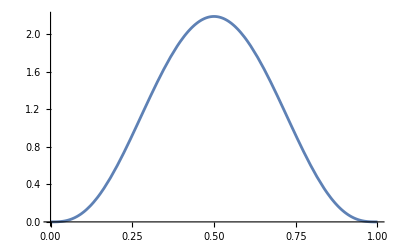

```mathematica
prior[p_]:=140 p^3(1-p)^3;
Plot[prior[p], {p, 0, 1}]
```

Three comments (more could be made):

(1) The factor of 140 in the definition is (as usual) there to make the area under the curve 1.
(2) We can make the curve more sharply peaked by putting in higher powers of p and 1-p.
(3) We can also make the curve asymmetrical by making the power of p and the power of 1-p unequal.

So a more general prior might be,

P(p)=A(a,b)(p^a(1-p))^b

The factor A(a,b) out front will be needed to make the area under the curve 1. Now let’s rewrite this a bit. Let a=α-1, and let b=β-1. Then we have:

P(p)=A(α-1,β-1)(p^(α-1)(1-p))^(β-1)

THAT DOESN’T HELP AT ALL, DOES IT, HE-HE. I actually know why they did it, so let’s just run with it. Also, they decided to rewrite the factor that was 140 when α=β=4 in the denominator as 1/140 (which is a great place for it) and call it B(α, β). FINE. Now we have,

P(p)=1/(B(α,β))(p^(α-1)(1-p))^(β-1)

It’s still just a prior, and there are lots of priors, each with a different α and β. Here’s the one with α=5 and β=3.

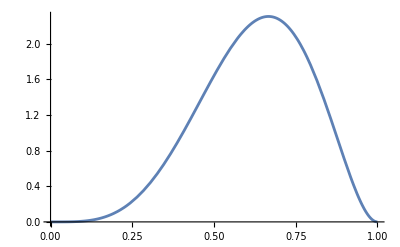

```mathematica
Plot[1/(1/105)p^(5-1)(1-p)^(3-1), {p, 0, 1}]
```

As two final important things to say about beta distributions: (1) P(p)=1/(B(α,β))(p^(α-1)(1-p))^(β-1) has mean μ=α/(α+β), and (2) it has variance σ^2=αβ/((α+β)^2(α+β+1)).

## For Problem Set 14

I do not yet have the bandwidth or perhaps even the creativity to create an interesting Problem Set 14. So there is no Problem Set 14 yet.

How about this for a non-problem-set problem set....

(1) How about you create some beta distributions for your own edification!? One that might be good would be one that has a specific mean, like 0.1. That would be appropriate for kicking a field goal from 80 yards out (see the graph on the next page). Under what circumstances might you not just want to stick p=0.1 into the binomial distribution? In other words, why would you first introduce hyperparameters to create a distribution in p? And only then ask what number of successful field goals is likely given a number of attempted field goals?

(2) Suppose you chose α=1 and β=9 in order to get μ=0.1. What is this beta function’s variance? What could you do to increase the variance if the function seemed to narrow?

(3) Instead of me creating an illustrative variation of the Shaq-gets-into-the-White-House problem, you could continue with the field goal goal problem. Given the distribution with α=1 and β=9, what if three field goal attempts from the 80-yard line are made by a particular player and one field goal is made? In other words, you now have a prior and a likelihood for this player’s field goal stats. Can you construct the posterior for this player?